```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\F Standard.xlsx"]
```

{{{0.04,0.1245},{0.08,0.285},{0.12,0.4435},{0.16,0.5425},{0.2,0.6315},{0.24,0.718},{0.28,0.7995},{0.32,0.8785}}}

```mathematica
da={{0.04,0.1245},{0.08,0.28500000000000003},{0.12,0.4435},{0.16,0.5425},{0.2,0.6315},{0.24,0.718},{0.28,0.7995000000000001},{0.32,0.8785000000000001}}
```

{{0.04,0.1245},{0.08,0.285},{0.12,0.4435},{0.16,0.5425},{0.2,0.6315},{0.24,0.718},{0.28,0.7995},{0.32,0.8785}}

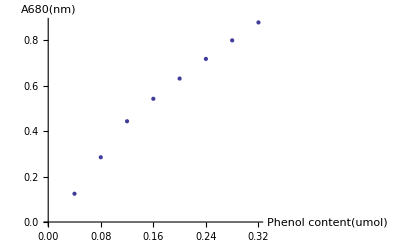

```mathematica
graph=ListPlot[da,AxesLabel->{"Phenol content(umol)","A680(nm)"}]
```

```mathematica
graph2=LinearModelFit[da,x,x]
```

```mathematica
Normal[graph2]
```

0.0834286+2.60804 x

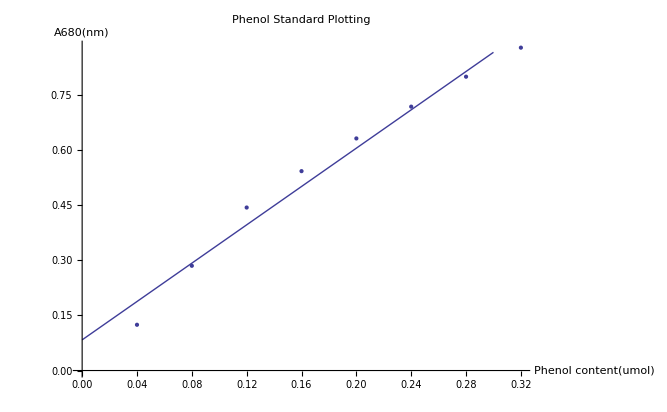

```mathematica
Show[graph,Plot[graph2[x],{x,0,0.3}],PlotLabel->"Phenol Standard Plotting"]
```

```mathematica
graph2["RSquared"]
```

0.977435

```mathematica
Solve[y==0.08342857142857123+2.6080357142857156 x,x]
```

{{x→-0.38343 (0.0834286-y)}}

```mathematica
a[b_]=-0.38343033207805527 (0.08342857142857123-b)
```

-0.38343 (0.0834286-b)

```mathematica
a[.184]
```

0.0385621

```mathematica
a[.214]
```

0.050065

```mathematica
a[.265]
```

0.06962

```mathematica
a[.3135]
```

0.0882164

```mathematica
a[.387]
```

0.116398

```mathematica
a[.438]
```

0.135953

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\v-s.xlsx"]
```

```mathematica
data2={{0.189,0.002570806666666667},{0.283,0.0033376666666666667},{0.472,0.004641333333333333},{0.755,0.005881093333333334},{1.132,0.007759866666666667},{2.358,0.009063533333333334}};
```

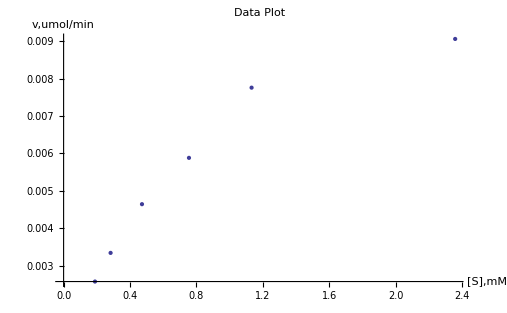

```mathematica
cs=ListPlot[data2,AxesLabel->{"[S],mM","v,umol/min"},PlotLabel->"Data Plot"]
```

```mathematica
nlm=NonlinearModelFit[data2,(a*x)/(x+b),{a,b},x]
```

```mathematica
Normal[nlm]
```

(0.0120434 x)/(0.728042+x)

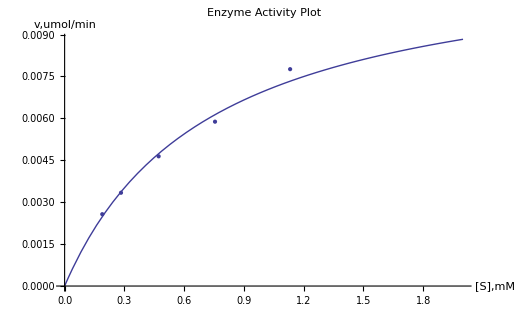

```mathematica
Show[Plot[nlm[x],{x,0,2}],cs,AxesLabel->{"[S],mM","v,umol/min"},PlotLabel->"Enzyme Activity Plot"]
```

```mathematica
nlm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0120434 | 0.000581252 | 20.7198 | 0.000032055
b | 0.728042 | 0.0816064 | 8.92138 | 0.000872757}

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\-s-v.xlsx"]
```

```mathematica
data3={{5.291005291005291,388.9829651393466},{3.53356890459364,299.6105063417557},{2.1186440677966103,215.45532892846884},{1.3245033112582782,170.03641046336054},{0.88339222614841,128.86819361157407},{0.4240882103477523,110.3322471736556}};
```

```mathematica
lm=LinearModelFit[data3,x,x]
```

```mathematica
Normal[lm]
```

87.1835+58.208 x

```mathematica
lm["ParameterTable"]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 87.1834691190921, 5.283881620079543, 16.499890684110298, 0.00007900713314440315}, {x, 58.207961568055595, 1.8743132704631214, 31.055620469289572, 6.40610930361506*^-6}}
```

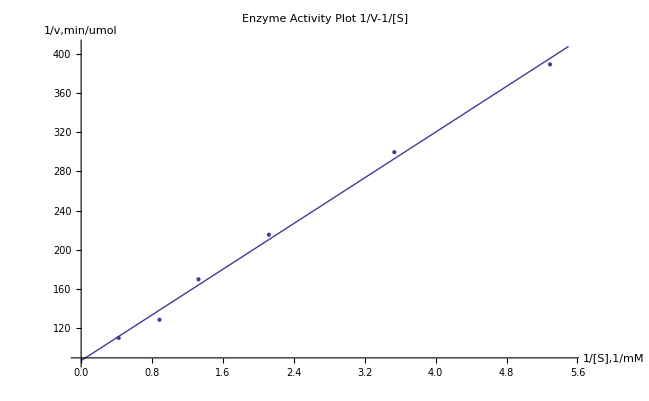

```mathematica
Show[Plot[lm[x],{x,0,5.5}],cs1=ListPlot[data3],AxesLabel->{"1/[S],1/mM","1/v,min/umol"},PlotLabel->"Enzyme Activity Plot 1/V-1/[S]"]
```